```mathematica
Parallel[a_,b_]:=1/((1/a) + (1/b))
```

```mathematica
XCap[C_]:=1/(2 * Pi*ω*C*I)
```

```mathematica
VoltageDivider[Top_,Bottom_]:=Bottom/(Top+Bottom)
```

```mathematica
T[k_]:=Norm[(Parallel[Rf,XCap[C]]/Rg)/.{ω->k,Rf->5100,Rg->5100,C->0.3*10^-9}]
```

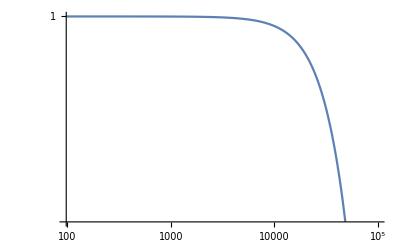

```mathematica
LogLogPlot[T[x],{x,0,100000}]
```

```mathematica
(* Find the 3db point *)
NSolve[T[x]== Sqrt[2]/2 &&x>0 ,x,Reals]
```

{{x→104023.}}